```mathematica
Nt = 551;
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;
Nx = 551; 
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

1.

```mathematica
rs = Table[0.01*i,{i,1,200}];

maxevalsCN = {};
maxevalsEuler = {};
maxevalsRK2 = {};
maxevalsRK4 = {};
maxevalsN = {};

maxevalsCN = Table[0,{i,1,Length[rs]}];
maxevalsEuler = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsRK4 = Table[0,{i,1,Length[rs]}];
maxevalsN = Table[0,{i,1,Length[rs]}];
```

```mathematica
Do[

deltat = deltax * rs[[p]];

h = (2*Pi)/ (Nx);

T = Array[#&,Nt,{ti,tf}]//N;

(*a = -2;
b = 8;*)

(*Equal X Spacing*)
(*X = Array[#&,Nx,{a,b}]//N*)

(*Equal X spacing that appears to be more accurate when transforming to [0,2pi]*)
(*X =  Table[xm = xi + m *deltax, {m, 0, Nx -1 }]//N*)

(*X spacing as defined in http://easymeca.mobile.basilisk.fr/sandbox/easystab/matlabdifmatsuite.pdf*)
X = Table[(i-1)*h,{i,1,Nx}]//N;

(*Transform X from [a,b] to [0,2pi]*)
(*X = ((X-a) * 2*Pi) / (b-a)*)

(************************************************************************************************************)

(*Derivative Matrix*)
D1 = Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}]//N;
D2 = MatrixPower[D1,2];
D3 = MatrixPower[D1, 3];
D4 = MatrixPower[D1,4];
DL = -c * D1 * deltat;

f[x_] =ⅇ^(- 4(x-π)^2);

(*Print["Max Difference is"<>ToString[Max[Abs[D1.F - f'[X]]]]];*)

(************************************************************************************************************)

(*CN*)
I1 = IdentityMatrix[Length[D1]];
A = I1 - ((DL / 2));
B = I1 + ((DL / 2));
M = Inverse[A].B;

(*Euler*)
Ieuler = IdentityMatrix[Length[D1]];
euler = Ieuler + DL;

(*RK2*)
IRK2 = IdentityMatrix[Length[D1]];
Mrk = (IRK2 + (DL) + ((1/2)* MatrixPower[DL,2]));

(*RK4*)
IRK4 = IdentityMatrix[Length[D1]];
MRK4 = IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4]));

(*LD2*)
IN = IdentityMatrix[Length[D1]];
AN = IN - ((DL / 2)) + (((MatrixPower[DL,2])/12));
BN = IN + ((DL / 2)) + (((MatrixPower[DL,2])/12));
MN = Inverse[AN].BN;

(************************************************************************************************************)

(*Eigenvalues*)

(*CN*)
evals = Abs[Eigenvalues[N[M]]];
maxevalsCN[[p]] = Max[evals];

(*Euler*)
evalsEuler = Abs[Eigenvalues[N[euler]]];
maxevalsEuler[[p]] = Max[evalsEuler];

(*RK2*)
evalsRK2 = Abs[Eigenvalues[N[Mrk]]];
maxevalsRK2[[p]] = Max[evalsRK2];

(*RK4*)
evalsRK4 = Abs[Eigenvalues[N[MRK4]]];
maxevalsRK4[[p]] = Max[evalsRK4];

(*New Method*)
evalsN = Abs[Eigenvalues[N[MN]]];
maxevalsN[[p]] = Max[evalsN];

,{p,1,Length[rs]}]
```

```mathematica
maxevalsCN = Join[{1},maxevalsCN];
rsCN = Join[{0},rs];

maxevalsEuler = Join[{1},maxevalsEuler];
rsEuler = Join[{0}, rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsRK4 = Join[{1},maxevalsRK4];
rsRK4 = Join[{0},rs];

maxevalsN = Join[{1},maxevalsN];
rsN = Join[{0},rs];

exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max_FDM.dat",exportData,"Table"];
```

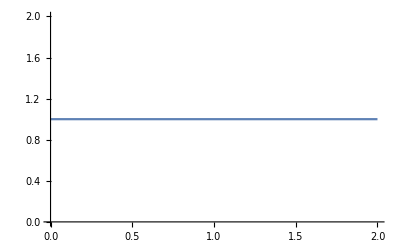

```mathematica
ListPlot[Transpose[{rsCN,maxevalsCN}], Joined->True]
```

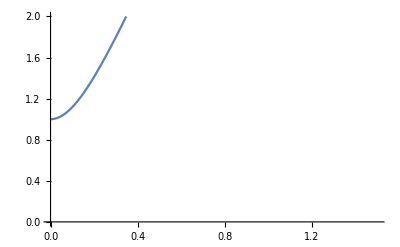

```mathematica
ListPlot[Transpose[{rsEuler,maxevalsEuler}], Joined->True, PlotRange->{{0,1.5},{0,2}}]
```

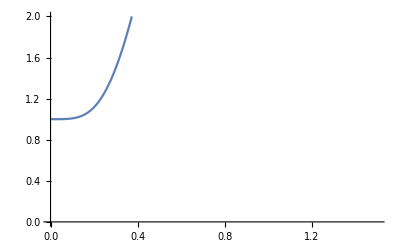

```mathematica
ListPlot[Transpose[{rsRK2,maxevalsRK2}], Joined->True, PlotRange->{{0,1.5},{0,2}}]
```

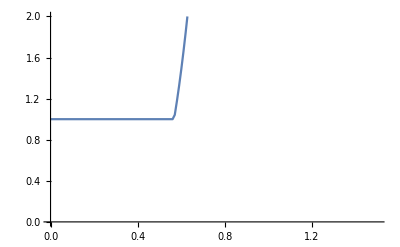

```mathematica
ListPlot[Transpose[{rsRK4,maxevalsRK4}], Joined->True, PlotRange->{{0,1.5},{0,2}}]
```

```mathematica
ListPlot[Transpose[{rsN,maxevalsN}], Joined->True]
```

-Graphics-

```mathematica
exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max_FDM.dat",exportData,"Table"];*)
```